```mathematica
pauliMatrix[0]={{1,0},{0,1}};
pauliMatrix[1]={{0,1},{1,0}};
pauliMatrix[2]={{0,-ⅈ},{ⅈ,0}};
pauliMatrix[3]={{1,0},{0,-1}};

(*Definition of the matrices ψ*)
DiracMatrix[i_Integer?Positive,Dimension->n_Integer?Positive]/;If[OddQ[n],n=!=i,True]:=Module[{ν=n/2},Which[i==1,KroneckerProduct@@Table[pauliMatrix[1],{ν}],

2 ν>i>1&&EvenQ[i],
KroneckerProduct[Sequence@@Table[pauliMatrix[1],{ν-i/2}],pauliMatrix[2],Sequence@@Table[pauliMatrix[0],{i/2-1}]],2 ν>i>1&&OddQ[i],KroneckerProduct[Sequence@@Table[pauliMatrix[1],{ν-(i-1)/2}],pauliMatrix[3],Sequence@@Table[pauliMatrix[0],{(i-1)/2-1}]],
i==2 ν,KroneckerProduct[pauliMatrix[2],Sequence@@Table[pauliMatrix[0],{ν-1}]]]]

DiracMatrix[i_Integer?Positive,Dimension->n_Integer?Positive]/;n==i&&OddQ[i]:=Module[{ν=(n-1)/2},(-I)^ν Dot@@Table[DiracMatrix[j,Dimension->n],{j,2ν}]]
```

```mathematica
n=10; (*The number of fermions in our system*)
s=(3!)/n^3 J^2;
J=100;
L = 2^(n/2);
dist= 1/(√(2π s))ⅇ^(-x^2/(2s)); 
gauss=ProbabilityDistribution[dist,{x,-Infinity, Infinity}];
random := RandomVariate[gauss];
```

```mathematica
iteration:=Module[{},
(*Generating the random coupling tensor Subscript[J, abcd]*)
tensorJ = Normal@ SymmetrizedArray[_ :> random, {n,n,n,n},Antisymmetric[All]];
(*Generates an array containing all Subscript[ψ, i] from i=1 to n*)
psi= Table[DiracMatrix[i,Dimension-> n],{i,n}]; 

(*Definition of the Hamiltonian*)
H=Sum[If[a<b <c<d, tensorJ[[a,b,c,d]]*psi[[a]].psi[[b]].psi[[c]].psi[[d]],0],{a,n},{b,n},{c,n},{d,n}];
evalH = Eigenvalues[H];
diagH = DiagonalMatrix[evalH];
Zt = Sum[ⅇ^(-(β+I*t)evalH[[i]]),{i,2^Floor[n/2]}];
Z= Sum[ⅇ^(-β*evalH[[i]]),{i,2^Floor[n/2]}];
{Zt,Z}]
```

```mathematica
iteration
```

{ⅇ^(-206.876 (-ⅈ t-β))+ⅇ^(-206.876 (-ⅈ t-β))+ⅇ^(-143.451 (-ⅈ t-β))+ⅇ^(-143.451 (-ⅈ t-β))+2 ⅇ^(-114.173 (-ⅈ t-β))+ⅇ^(-82.1133 (-ⅈ t-β))+ⅇ^(-82.1133 (-ⅈ t-β))+ⅇ^(-65.9369 (-ⅈ t-β))+ⅇ^(-65.9369 (-ⅈ t-β))+2 ⅇ^(-54.9957 (-ⅈ t-β))+ⅇ^(-20.7406 (-ⅈ t-β))+ⅇ^(-20.7406 (-ⅈ t-β))+ⅇ^(-10.36 (-ⅈ t-β))+ⅇ^(-10.36 (-ⅈ t-β))+ⅇ^(4.39131 (-ⅈ t-β))+ⅇ^(4.39131 (-ⅈ t-β))+ⅇ^(24.5255 (-ⅈ t-β))+ⅇ^(24.5255 (-ⅈ t-β))+ⅇ^(49.6258 (-ⅈ t-β))+ⅇ^(49.6258 (-ⅈ t-β))+2 ⅇ^(67.8443 (-ⅈ t-β))+2 ⅇ^(104.201 (-ⅈ t-β))+2 ⅇ^(117.413 (-ⅈ t-β))+ⅇ^(157.391 (-ⅈ t-β))+ⅇ^(157.391 (-ⅈ t-β))+ⅇ^(173.255 (-ⅈ t-β))+ⅇ^(173.255 (-ⅈ t-β)),ⅇ^(-173.255 β)+ⅇ^(-173.255 β)+ⅇ^(-157.391 β)+ⅇ^(-157.391 β)+2 ⅇ^(-117.413 β)+2 ⅇ^(-104.201 β)+2 ⅇ^(-67.8443 β)+ⅇ^(-49.6258 β)+ⅇ^(-49.6258 β)+ⅇ^(-24.5255 β)+ⅇ^(-24.5255 β)+ⅇ^(-4.39131 β)+ⅇ^(-4.39131 β)+ⅇ^(10.36 β)+ⅇ^(10.36 β)+ⅇ^(20.7406 β)+ⅇ^(20.7406 β)+2 ⅇ^(54.9957 β)+ⅇ^(65.9369 β)+ⅇ^(65.9369 β)+ⅇ^(82.1133 β)+ⅇ^(82.1133 β)+2 ⅇ^(114.173 β)+ⅇ^(143.451 β)+ⅇ^(143.451 β)+ⅇ^(206.876 β)+ⅇ^(206.876 β)}

```mathematica
samples=90;
β=5;
Zfuncs= Table[iteration,samples];
```

$Aborted

```mathematica
avgZt= Sum[Zfuncs[[i,1]]*Conjugate[Zfuncs[[i,1]]],{i,samples}]/samples;
avgZ = Sum[Zfuncs[[i,2]],{i,samples}]/samples;
```

```mathematica
gt=avgZt/(avgZ)^2;
```

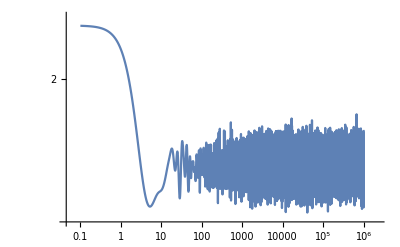

```mathematica
LogLogPlot[gt,{t,0.1,10^6},PlotPoints->500]
```